```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3, 0≤x≤1}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3, 1<x≤2}, {Subscript[c, 2,1](x-2)+Subscript[c, 2,2](x-2)^2+Subscript[c, 2,3](x-2)^3, 2<x≤3}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3],Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3]};
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
I3=f[3]
```

1+c_(0,1)+c_(0,2)+c_(0,3)

c_(1,1)+c_(1,2)+c_(1,3)

c_(2,1)+c_(2,2)+c_(2,3)

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(k=-2)^3 f[x-k],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[∑_(k=-2)^3 k f[x-k],x>0&&x<1],x]
```

{2+c_(0,1)+c_(0,2)+c_(0,3)+c_(1,1)+c_(1,2)+c_(1,3)+c_(2,1)+c_(2,2)+c_(2,3),-2 c_(0,2)-3 c_(0,3)-2 c_(1,2)-3 c_(1,3)-2 c_(2,2)-3 c_(2,3),2 c_(0,2)+3 c_(0,3)+2 c_(1,2)+3 c_(1,3)+2 c_(2,2)+3 c_(2,3)}

{1+c_(0,1)+c_(0,2)+c_(0,3)+2 c_(1,1)+2 c_(1,2)+2 c_(1,3)+3 c_(2,1)+3 c_(2,2)+3 c_(2,3),-c_(0,1)-2 c_(0,2)-3 c_(0,3)-3 c_(1,1)-4 c_(1,2)-6 c_(1,3)-5 c_(2,1)-6 c_(2,2)-9 c_(2,3),c_(0,2)+3 c_(0,3)+c_(1,2)+6 c_(1,3)+c_(2,2)+9 c_(2,3),-c_(0,3)-3 c_(1,3)-5 c_(2,3)}

```mathematica
(*Smoothness*)
Dh=Simplify[D[h[x],x],x>0];
S0=(Dh/.x->0)==0
S1=Limit[Dh,x->1,Direction->1]==Limit[Dh,x->1,Direction->-1]
S2=Limit[Dh,x->2,Direction->1]==Limit[Dh,x->2,Direction->-1]
S3=Limit[Dh,x->3,Direction->1]==Limit[Dh,x->3,Direction->-1]
```

c_(0,1)==0

c_(0,1)+2 c_(0,2)+3 c_(0,3)==c_(1,1)

c_(1,1)+2 c_(1,2)+3 c_(1,3)==c_(2,1)

c_(2,1)+2 c_(2,2)+3 c_(2,3)==0

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	I3==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0,
	S0,S1,S2,S3
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,1)→0,c_(0,3)→-1-c_(0,2),c_(1,1)→-3-c_(0,2),c_(1,2)→19/4+(3 c_(0,2))/2,c_(1,3)→-7/4-(c_(0,2))/2,c_(2,1)→5/4+(c_(0,2))/2,c_(2,2)→-5/2-c_(0,2),c_(2,3)→5/4+(c_(0,2))/2}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-4,7}]
```

{{-2,3},{-2,2},{-1,2},{-1,1},{0,1},{0,0},{1,0},{1,-1},{2,-1},{2,-2},{3,-2},{3,-3}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-5)^6 ∑_(j=-5)^6 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]]
```

(92669325+117493344 c_(0,2)+52220952 c_(0,2)^2+9325760 c_(0,2)^3+598096 c_(0,2)^4)/25804800

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=Solve[DErr==0,FreeVars,Reals];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1 | 0.0575003 | True

```mathematica
RootReduce[Sols[[1]]]
```

{c_(0,2)→Root[7343334+6527619 #1+1748580 #1^2+149524 #1^3&,1]}

{c_(0,1)→0,c_(0,3)→1.06787,c_(1,1)→-0.932133,c_(1,2)→1.6482,c_(1,3)→-0.716067,c_(2,1)→0.216067,c_(2,2)→-0.432133,c_(2,3)→0.216067,c_(0,2)→-2.06787}

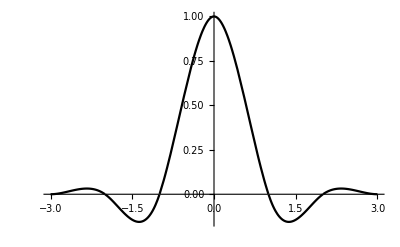

```mathematica
NSol=N[Sols[[1]]];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```